## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PFK1";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_PFK1_test";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(atp^c+f6p^c⇌adp^c+fdp^c+h^c)^PFK1

Bi Bi (iso-ordered); [f6p,atp,fdp,adp]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp,Null;f6p,Null | 1 | 0.95
1.05 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 0.00009 | 0.000054
0.000126 | gdp | 0.001
f6p | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 | 
1 | gdp | 0.0042 | 0.00293
0.00547 | f6p | 0.00004
atp | 0.005 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | 0.00009 | 0.000054
0.000126 | gdp | 0.001
atp | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | gdp | 0.001
atp | Null
f6p | Null | 110.7 | 108.1
113.3 | 1/s | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kinc | pep | 0.00075 | 0.0007
0.0008 |  | NonCompetitive | atp | 0.00009
NonCompetitive | f6p | 0.00009 | M | 8.5 | 28 | tris | 0.05 | 
1 | Kic | adp | 0.0002 | 0.00019
0.00021 |  | Competitive | atp | 0.00009 | M | 8.5 | 28 | tris | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ka | adp | 0.000025 | 0.00002375
0.00002625 |  |  | M | 8.5 | 28 | tris | 0.05 | 
1 | Ka | gdp | 0.00004 | 0.000035
0.000045 |  |  | M | 8.5 | 28 | tris | 0.05 |

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | f6p | 2.11 | 2.
2.22 | gdp | 0.001
atp | 0.001 |  | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 | 
1 | L0 |  | 4000000 | 3.8×10^6
4.2×10^6 |  |  | 8.5 | 28 | tris | 0.05 |

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {0,0};
s05Priorities = {1};
kcatPriorities = {0};
inhibitionPriorities={0, 0};
activationPriorities = {0, 0};
otherParamsPriorities = {1,0};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(atp^c+f6p^c⇌adp^c+fdp^c+h^c)^PFK1

Bi Bi (iso-ordered); [f6p,atp,fdp,adp]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp,Null;f6p,Null | 1 | 0.95
1.05 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | 0.00009 | 0.000054
0.000126 | gdp | 0.001
atp | 0.001 | M | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | f6p | 2.11 | 2.
2.22 | gdp | 0.001
atp | 0.001 |  | 8.5 | 30 | detam | 0.051
netmphn | 0.051
mes | 0.1 |

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
(*catalyticBranch={"E_PFK1[c] + atp[c] <=> E_PFK1[c]&atp",
				"E_PFK1[c]&atp + f6p[c] <=> E_PFK1[c]&atp&f6p",
				
				"E_PFK1[c] + f6p[c] <=> E_PFK1[c]&f6p",
				"E_PFK1[c]&f6p + atp[c] <=> E_PFK1[c]&atp&f6p",

				"E_PFK1[c]&atp&f6p <=> E_PFK1[c]&fdp&adp",
				
				"E_PFK1[c]&fdp&adp <=> E_PFK1[c]&fdp + adp[c]",
				"E_PFK1[c]&fdp <=> E_PFK1[c] + fdp[c]"};*)

catalyticBranch={"E_PFK1[c] + f6p[c] <=> E_PFK1[c]&f6p",
				"E_PFK1[c]&f6p + atp[c] <=> E_PFK1[c]&atp&f6p",

				"E_PFK1[c]&atp&f6p <=> E_PFK1[c]&fdp&adp",
				
				"E_PFK1[c]&fdp&adp <=> E_PFK1[c]&fdp + adp[c]",
				"E_PFK1[c]&fdp <=> E_PFK1[c] + fdp[c]"};

enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{m["gdp", "c"]},ActivationSites->4,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PFK1^c)_^+f6p^c⇌(PFK1^c&f6p^c)_^)^PFK11,((PFK1^c&fdp^c)_^⇌(PFK1^c)_^+fdp^c)^PFK12,((PFK1^c&f6p^c)_^+atp^c⇌(PFK1^c&atp^c&f6p^c)_^)^PFK13,((PFK1^c&fdp^c&adp^c)_^⇌(PFK1^c&fdp^c)_^+adp^c)^PFK14,((PFK1^c&atp^c&f6p^c)_^⇌(PFK1^c&fdp^c&adp^c)_^)^PFK15,((PFK1^c)_^(gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c))^PFK11$3,((PFK1^c&fdp^c)_^(gdp^c)⇌(PFK1^c)_^(gdp^c)+fdp^c)^PFK12$3,((PFK1^c&f6p^c)_^(gdp^c)+atp^c⇌(PFK1^c&atp^c&f6p^c)_^(gdp^c))^PFK13$3,((PFK1^c&fdp^c&adp^c)_^(gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c)+adp^c)^PFK14$3,((PFK1^c&atp^c&f6p^c)_^(gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c))^PFK15$3,((PFK1^c)_^(gdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^c))^PFK11$7,((PFK1^c&fdp^c)_^(gdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^c)+fdp^c)^PFK12$7,((PFK1^c&f6p^c)_^(gdp^cgdp^c)+atp^c⇌(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^c))^PFK13$7,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^c)+adp^c)^PFK14$7,((PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c))^PFK15$7,((PFK1^c)_^(gdp^cgdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c))^PFK11$8,((PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^cgdp^c)+fdp^c)^PFK12$8,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)+atp^c⇌(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^c))^PFK13$8,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)+adp^c)^PFK14$8,((PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c))^PFK15$8,((PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK11$10,((PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+fdp^c)^PFK12$10,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)+atp^c⇌(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK13$10,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)+adp^c)^PFK14$10,((PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK15$10,((PFK1^c)_^+gdp^c⇌(PFK1^c)_^(gdp^c))^PFK1_Activation_gdp$11,((PFK1^c)_^(gdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^c))^PFK1_Activation_gdp$12,((PFK1^c)_^(gdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^c))^PFK1_Activation_gdp$14,((PFK1^c)_^(gdp^cgdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Activation_gdp$15}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PFK1^c)_^+f6p^c⇌(PFK1^c&f6p^c)_^)^PFK11,Overscript[(PFK1^c&fdp^c)_^⇌(PFK1^c)_^+fdp^c, PFK12],((PFK1^c&f6p^c)_^+atp^c⇌(PFK1^c&atp^c&f6p^c)_^)^PFK13,Overscript[(PFK1^c&fdp^c&adp^c)_^⇌(PFK1^c&fdp^c)_^+adp^c, PFK14],((PFK1^c&atp^c&f6p^c)_^⇌(PFK1^c&fdp^c&adp^c)_^)^PFK15};
catalyticReactionsSet2 ={Overscript[(PFK1^c)_^(adp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(adp^c), PFK11$14],Overscript[(PFK1^c&fdp^c)_^(adp^c)⇌(PFK1^c)_^(adp^c)+fdp^c, PFK12$14],Overscript[(PFK1^c&f6p^c)_^(adp^c)+atp^c⇌(PFK1^c&atp^c&f6p^c)_^(adp^c), PFK13$14],Overscript[(PFK1^c&fdp^c&adp^c)_^(adp^c)⇌(PFK1^c&fdp^c)_^(adp^c)+adp^c, PFK14$14],Overscript[(PFK1^c&atp^c&f6p^c)_^(adp^c)⇌(PFK1^c&fdp^c&adp^c)_^(adp^c), PFK15$14]};

catalyticReactionsSet3 ={ Overscript[(PFK1^c)_^(gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c), PFK11$15],Overscript[(PFK1^c&fdp^c)_^(gdp^c)⇌(PFK1^c)_^(gdp^c)+fdp^c, PFK12$15],Overscript[(PFK1^c&f6p^c)_^(gdp^c)+atp^c⇌(PFK1^c&atp^c&f6p^c)_^(gdp^c), PFK13$15],Overscript[(PFK1^c&fdp^c&adp^c)_^(gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c)+adp^c, PFK14$15],Overscript[(PFK1^c&atp^c&f6p^c)_^(gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c), PFK15$15]};
catalyticReactionsSetsList = {catalyticReactionsSet1, catalyticReactionsSet2};
```

### Setup King-Altman Equations

#### Define some parameters

```mathematica
MWCFlag=True;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=30;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={(*{"prod_inhib_adp",fdp^c->0}*)};
otherMetsForwardZeroSub={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,{(*inhibitionList[[2]])*)}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{atp^c→1/10000000000,f6p^c→1/10000000000}

{adp^c→1/10000000000,fdp^c→1/10000000000}

{atp^c→∞,f6p^c→∞}

{adp^c→∞,fdp^c→∞}

-(PFK1^c&fdp^c&adp^c)_^ k_PFK15^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^c) k_PFK15^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c) k_PFK15^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c) k_PFK15^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK15^⟵+(PFK1^c&atp^c&f6p^c)_^ k_PFK15^⟶+(PFK1^c&atp^c&f6p^c)_^(gdp^c) k_PFK15^⟶+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^c) k_PFK15^⟶+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^c) k_PFK15^⟶+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK15^⟶

1

2

{(PFK1^c&f6p^c)_^ k_PFK11^⟵+(PFK1^c&fdp^c)_^ k_PFK12^⟶+(PFK1^c)_^(gdp^c) k_PFK1_Activation_gdp^⟵==(PFK1^c)_^ (f6p^c k_PFK11^⟶+fdp^c k_PFK12^⟵+4 gdp^c k_PFK1_Activation_gdp^⟶),(PFK1^c&f6p^c)_^(gdp^c) k_PFK11^⟵+(PFK1^c&fdp^c)_^(gdp^c) k_PFK12^⟶+2 (PFK1^c)_^(gdp^cgdp^c) k_PFK1_Activation_gdp^⟵+4 (PFK1^c)_^ gdp^c k_PFK1_Activation_gdp^⟶==(PFK1^c)_^(gdp^c) (f6p^c k_PFK11^⟶+fdp^c k_PFK12^⟵+k_PFK1_Activation_gdp^⟵+3 gdp^c k_PFK1_Activation_gdp^⟶),(PFK1^c&f6p^c)_^(gdp^cgdp^c) k_PFK11^⟵+(PFK1^c&fdp^c)_^(gdp^cgdp^c) k_PFK12^⟶+3 (PFK1^c)_^(gdp^cgdp^cgdp^c) k_PFK1_Activation_gdp^⟵+3 (PFK1^c)_^(gdp^c) gdp^c k_PFK1_Activation_gdp^⟶==(PFK1^c)_^(gdp^cgdp^c) (f6p^c k_PFK11^⟶+fdp^c k_PFK12^⟵+2 k_PFK1_Activation_gdp^⟵+2 gdp^c k_PFK1_Activation_gdp^⟶),(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c) k_PFK11^⟵+(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c) k_PFK12^⟶+4 (PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK1_Activation_gdp^⟵+2 (PFK1^c)_^(gdp^cgdp^c) gdp^c k_PFK1_Activation_gdp^⟶==(PFK1^c)_^(gdp^cgdp^cgdp^c) (f6p^c k_PFK11^⟶+fdp^c k_PFK12^⟵+3 k_PFK1_Activation_gdp^⟵+gdp^c k_PFK1_Activation_gdp^⟶),(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK11^⟵+(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK12^⟶+(PFK1^c)_^(gdp^cgdp^cgdp^c) gdp^c k_PFK1_Activation_gdp^⟶==(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c) (f6p^c k_PFK11^⟶+fdp^c k_PFK12^⟵+4 k_PFK1_Activation_gdp^⟵),(PFK1^c)_^ f6p^c k_PFK11^⟶+(PFK1^c&atp^c&f6p^c)_^ k_PFK13^⟵-(PFK1^c&f6p^c)_^ (k_PFK11^⟵+atp^c k_PFK13^⟶)==0,(PFK1^c)_^(gdp^c) f6p^c k_PFK11^⟶+(PFK1^c&atp^c&f6p^c)_^(gdp^c) k_PFK13^⟵-(PFK1^c&f6p^c)_^(gdp^c) (k_PFK11^⟵+atp^c k_PFK13^⟶)==0,(PFK1^c)_^(gdp^cgdp^c) f6p^c k_PFK11^⟶+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^c) k_PFK13^⟵-(PFK1^c&f6p^c)_^(gdp^cgdp^c) (k_PFK11^⟵+atp^c k_PFK13^⟶)==0,(PFK1^c)_^(gdp^cgdp^cgdp^c) f6p^c k_PFK11^⟶+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^c) k_PFK13^⟵-(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c) (k_PFK11^⟵+atp^c k_PFK13^⟶)==0,(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c) f6p^c k_PFK11^⟶+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK13^⟵-(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c) (k_PFK11^⟵+atp^c k_PFK13^⟶)==0,(PFK1^c)_^ fdp^c k_PFK12^⟵-(PFK1^c&fdp^c)_^ (k_PFK12^⟶+adp^c k_PFK14^⟵)+(PFK1^c&fdp^c&adp^c)_^ k_PFK14^⟶==0,(PFK1^c)_^(gdp^c) fdp^c k_PFK12^⟵-(PFK1^c&fdp^c)_^(gdp^c) (k_PFK12^⟶+adp^c k_PFK14^⟵)+(PFK1^c&fdp^c&adp^c)_^(gdp^c) k_PFK14^⟶==0,(PFK1^c)_^(gdp^cgdp^c) fdp^c k_PFK12^⟵-(PFK1^c&fdp^c)_^(gdp^cgdp^c) (k_PFK12^⟶+adp^c k_PFK14^⟵)+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c) k_PFK14^⟶==0,(PFK1^c)_^(gdp^cgdp^cgdp^c) fdp^c k_PFK12^⟵-(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c) (k_PFK12^⟶+adp^c k_PFK14^⟵)+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c) k_PFK14^⟶==0,(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c) fdp^c k_PFK12^⟵-(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c) (k_PFK12^⟶+adp^c k_PFK14^⟵)+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK14^⟶==0,(PFK1^c&f6p^c)_^ atp^c k_PFK13^⟶+(PFK1^c&fdp^c&adp^c)_^ k_PFK15^⟵-(PFK1^c&atp^c&f6p^c)_^ (k_PFK13^⟵+k_PFK15^⟶)==0,(PFK1^c&f6p^c)_^(gdp^c) atp^c k_PFK13^⟶+(PFK1^c&fdp^c&adp^c)_^(gdp^c) k_PFK15^⟵-(PFK1^c&atp^c&f6p^c)_^(gdp^c) (k_PFK13^⟵+k_PFK15^⟶)==0,(PFK1^c&f6p^c)_^(gdp^cgdp^c) atp^c k_PFK13^⟶+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c) k_PFK15^⟵-(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^c) (k_PFK13^⟵+k_PFK15^⟶)==0,(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c) atp^c k_PFK13^⟶+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c) k_PFK15^⟵-(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^c) (k_PFK13^⟵+k_PFK15^⟶)==0,(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c) atp^c k_PFK13^⟶+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK15^⟵-(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c) (k_PFK13^⟵+k_PFK15^⟶)==0,(PFK1^c&fdp^c)_^ adp^c k_PFK14^⟵-(PFK1^c&fdp^c&adp^c)_^ (k_PFK14^⟶+k_PFK15^⟵)+(PFK1^c&atp^c&f6p^c)_^ k_PFK15^⟶==0,(PFK1^c&fdp^c)_^(gdp^c) adp^c k_PFK14^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^c) (k_PFK14^⟶+k_PFK15^⟵)+(PFK1^c&atp^c&f6p^c)_^(gdp^c) k_PFK15^⟶==0,(PFK1^c&fdp^c)_^(gdp^cgdp^c) adp^c k_PFK14^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c) (k_PFK14^⟶+k_PFK15^⟵)+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^c) k_PFK15^⟶==0,(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c) adp^c k_PFK14^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c) (k_PFK14^⟶+k_PFK15^⟵)+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^c) k_PFK15^⟶==0,(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c) adp^c k_PFK14^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c) (k_PFK14^⟶+k_PFK15^⟵)+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK15^⟶==0}

{{(PFK1^c&f6p^c)_^ k_PFK11^⟵+(PFK1^c&fdp^c)_^ k_PFK12^⟶+(PFK1^c)_^(gdp^c) k_PFK1_Activation_gdp^⟵==(PFK1^c)_^ (f6p^c k_PFK11^⟶+fdp^c k_PFK12^⟵+4 gdp^c k_PFK1_Activation_gdp^⟶),(PFK1^c&f6p^c)_^(gdp^c) k_PFK11^⟵+(PFK1^c&fdp^c)_^(gdp^c) k_PFK12^⟶+2 (PFK1^c)_^(gdp^cgdp^c) k_PFK1_Activation_gdp^⟵+4 (PFK1^c)_^ gdp^c k_PFK1_Activation_gdp^⟶==(PFK1^c)_^(gdp^c) (f6p^c k_PFK11^⟶+fdp^c k_PFK12^⟵+k_PFK1_Activation_gdp^⟵+3 gdp^c k_PFK1_Activation_gdp^⟶),(PFK1^c&f6p^c)_^(gdp^cgdp^c) k_PFK11^⟵+(PFK1^c&fdp^c)_^(gdp^cgdp^c) k_PFK12^⟶+3 (PFK1^c)_^(gdp^cgdp^cgdp^c) k_PFK1_Activation_gdp^⟵+3 (PFK1^c)_^(gdp^c) gdp^c k_PFK1_Activation_gdp^⟶==(PFK1^c)_^(gdp^cgdp^c) (f6p^c k_PFK11^⟶+fdp^c k_PFK12^⟵+2 k_PFK1_Activation_gdp^⟵+2 gdp^c k_PFK1_Activation_gdp^⟶),(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c) k_PFK11^⟵+(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c) k_PFK12^⟶+4 (PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK1_Activation_gdp^⟵+2 (PFK1^c)_^(gdp^cgdp^c) gdp^c k_PFK1_Activation_gdp^⟶==(PFK1^c)_^(gdp^cgdp^cgdp^c) (f6p^c k_PFK11^⟶+fdp^c k_PFK12^⟵+3 k_PFK1_Activation_gdp^⟵+gdp^c k_PFK1_Activation_gdp^⟶),(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK11^⟵+(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK12^⟶+(PFK1^c)_^(gdp^cgdp^cgdp^c) gdp^c k_PFK1_Activation_gdp^⟶==(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c) (f6p^c k_PFK11^⟶+fdp^c k_PFK12^⟵+4 k_PFK1_Activation_gdp^⟵),(PFK1^c)_^ f6p^c k_PFK11^⟶+(PFK1^c&atp^c&f6p^c)_^ k_PFK13^⟵-(PFK1^c&f6p^c)_^ (k_PFK11^⟵+atp^c k_PFK13^⟶)==0,(PFK1^c)_^(gdp^c) f6p^c k_PFK11^⟶+(PFK1^c&atp^c&f6p^c)_^(gdp^c) k_PFK13^⟵-(PFK1^c&f6p^c)_^(gdp^c) (k_PFK11^⟵+atp^c k_PFK13^⟶)==0,(PFK1^c)_^(gdp^cgdp^c) f6p^c k_PFK11^⟶+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^c) k_PFK13^⟵-(PFK1^c&f6p^c)_^(gdp^cgdp^c) (k_PFK11^⟵+atp^c k_PFK13^⟶)==0,(PFK1^c)_^(gdp^cgdp^cgdp^c) f6p^c k_PFK11^⟶+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^c) k_PFK13^⟵-(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c) (k_PFK11^⟵+atp^c k_PFK13^⟶)==0,(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c) f6p^c k_PFK11^⟶+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK13^⟵-(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c) (k_PFK11^⟵+atp^c k_PFK13^⟶)==0,(PFK1^c)_^ fdp^c k_PFK12^⟵-(PFK1^c&fdp^c)_^ (k_PFK12^⟶+adp^c k_PFK14^⟵)+(PFK1^c&fdp^c&adp^c)_^ k_PFK14^⟶==0,(PFK1^c)_^(gdp^c) fdp^c k_PFK12^⟵-(PFK1^c&fdp^c)_^(gdp^c) (k_PFK12^⟶+adp^c k_PFK14^⟵)+(PFK1^c&fdp^c&adp^c)_^(gdp^c) k_PFK14^⟶==0,(PFK1^c)_^(gdp^cgdp^c) fdp^c k_PFK12^⟵-(PFK1^c&fdp^c)_^(gdp^cgdp^c) (k_PFK12^⟶+adp^c k_PFK14^⟵)+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c) k_PFK14^⟶==0,(PFK1^c)_^(gdp^cgdp^cgdp^c) fdp^c k_PFK12^⟵-(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c) (k_PFK12^⟶+adp^c k_PFK14^⟵)+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c) k_PFK14^⟶==0,(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c) fdp^c k_PFK12^⟵-(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c) (k_PFK12^⟶+adp^c k_PFK14^⟵)+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK14^⟶==0,(PFK1^c&f6p^c)_^ atp^c k_PFK13^⟶+(PFK1^c&fdp^c&adp^c)_^ k_PFK15^⟵-(PFK1^c&atp^c&f6p^c)_^ (k_PFK13^⟵+k_PFK15^⟶)==0,(PFK1^c&f6p^c)_^(gdp^c) atp^c k_PFK13^⟶+(PFK1^c&fdp^c&adp^c)_^(gdp^c) k_PFK15^⟵-(PFK1^c&atp^c&f6p^c)_^(gdp^c) (k_PFK13^⟵+k_PFK15^⟶)==0,(PFK1^c&f6p^c)_^(gdp^cgdp^c) atp^c k_PFK13^⟶+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c) k_PFK15^⟵-(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^c) (k_PFK13^⟵+k_PFK15^⟶)==0,(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c) atp^c k_PFK13^⟶+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c) k_PFK15^⟵-(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^c) (k_PFK13^⟵+k_PFK15^⟶)==0,(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c) atp^c k_PFK13^⟶+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK15^⟵-(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c) (k_PFK13^⟵+k_PFK15^⟶)==0,(PFK1^c&fdp^c)_^ adp^c k_PFK14^⟵-(PFK1^c&fdp^c&adp^c)_^ (k_PFK14^⟶+k_PFK15^⟵)+(PFK1^c&atp^c&f6p^c)_^ k_PFK15^⟶==0,(PFK1^c&fdp^c)_^(gdp^c) adp^c k_PFK14^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^c) (k_PFK14^⟶+k_PFK15^⟵)+(PFK1^c&atp^c&f6p^c)_^(gdp^c) k_PFK15^⟶==0,(PFK1^c&fdp^c)_^(gdp^cgdp^c) adp^c k_PFK14^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c) (k_PFK14^⟶+k_PFK15^⟵)+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^c) k_PFK15^⟶==0,(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c) adp^c k_PFK14^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c) (k_PFK14^⟶+k_PFK15^⟵)+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^c) k_PFK15^⟶==0,(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c) adp^c k_PFK14^⟵-(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c) (k_PFK14^⟶+k_PFK15^⟵)+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c) k_PFK15^⟶==0,PFK1_total_Global==(PFK1^c)_^+(PFK1^c)_^(gdp^c)+(PFK1^c)_^(gdp^cgdp^c)+(PFK1^c)_^(gdp^cgdp^cgdp^c)+(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+(PFK1^c&f6p^c)_^+(PFK1^c&f6p^c)_^(gdp^c)+(PFK1^c&f6p^c)_^(gdp^cgdp^c)+(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)+(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)+(PFK1^c&fdp^c)_^+(PFK1^c&fdp^c)_^(gdp^c)+(PFK1^c&fdp^c)_^(gdp^cgdp^c)+(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)+(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)+(PFK1^c&atp^c&f6p^c)_^+(PFK1^c&atp^c&f6p^c)_^(gdp^c)+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^c)+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^c)+(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)+(PFK1^c&fdp^c&adp^c)_^+(PFK1^c&fdp^c&adp^c)_^(gdp^c)+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c)+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c)+(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)},{(PFK1^c)_^,(PFK1^c)_^(gdp^c),(PFK1^c)_^(gdp^cgdp^c),(PFK1^c)_^(gdp^cgdp^cgdp^c),(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c),(PFK1^c&f6p^c)_^,(PFK1^c&f6p^c)_^(gdp^c),(PFK1^c&f6p^c)_^(gdp^cgdp^c),(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c),(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c),(PFK1^c&fdp^c)_^,(PFK1^c&fdp^c)_^(gdp^c),(PFK1^c&fdp^c)_^(gdp^cgdp^c),(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c),(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c),(PFK1^c&atp^c&f6p^c)_^,(PFK1^c&atp^c&f6p^c)_^(gdp^c),(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^c),(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^c),(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c),(PFK1^c&fdp^c&adp^c)_^,(PFK1^c&fdp^c&adp^c)_^(gdp^c),(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c),(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c),(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)}}

3

102.62551

4

0.085895

5

0.005608

Simplifying...

Simplify::time: Time spent on a transformation exceeded 30. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

6

1033.47261

{(PFK1^c)_^≥0.,(PFK1^c)_^(gdp^c)≥0.,(PFK1^c)_^(gdp^cgdp^c)≥0.,(PFK1^c)_^(gdp^cgdp^cgdp^c)≥0.,(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)≥0.,(PFK1^c&f6p^c)_^≥0.,(PFK1^c&f6p^c)_^(gdp^c)≥0.,(PFK1^c&f6p^c)_^(gdp^cgdp^c)≥0.,(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)≥0.,(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)≥0.,(PFK1^c&fdp^c)_^≥0.,(PFK1^c&fdp^c)_^(gdp^c)≥0.,(PFK1^c&fdp^c)_^(gdp^cgdp^c)≥0.,(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)≥0.,(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)≥0.,(PFK1^c&atp^c&f6p^c)_^≥0.,(PFK1^c&atp^c&f6p^c)_^(gdp^c)≥0.,(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^c)≥0.,(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^c)≥0.,(PFK1^c&atp^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)≥0.,(PFK1^c&fdp^c&adp^c)_^≥0.,(PFK1^c&fdp^c&adp^c)_^(gdp^c)≥0.,(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c)≥0.,(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c)≥0.,adp^c≥0.,gdp^c≥0.,(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)≥0.,atp^c≥0.,f6p^c≥0.,fdp^c≥0.}

kcat for

kcat rev

km for

Simplifying...

km rev

Simplifying...

otherMetsReverseZeroSub

otherMetsForwardZeroSub

## Semi-Automated Simulate Data

```mathematica
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
Export["PFK1SimulateDataArguments.mx",{enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];
Export["PFK1SimulateDataResults.mx",{allFittingData, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
s05List
```

{{1,f6p,0.00009,{0.000054,0.000126},{{gdp,0.001},{atp,0.001}},M,8.5,30,{{detam,0.051},{netmphn,0.051},{mes,0.1}},{}}}

```mathematica
otherParmsList[[1,3]]="f6p"
```

f6p

```mathematica
otherParmsList
```

{{1,n,f6p,2.11,{2.,2.22},{{gdp,0.001},{atp,0.001}},,8.5,30,{{detam,0.051},{netmphn,0.051},{mes,0.1}},{}}}

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

```mathematica
FilePrint@dataPathList
```

Priority	adp[c]	gdp[c]	atp[c]	f6p[c]	fdp[c]	param_PFK1_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0.001	0.001	9.000000000000007e-6	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.007702679340006974
1	0	0.001	0.001	0.000014264038732150038	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.020099351492257313
1	0	0.001	0.001	0.000022606977883586257	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.051413474162681154
1	0	0.001	0.001	0.00003582964534981475	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.12527679844770145
1	0	0.001	0.001	0.00005678616100321741	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.27454359645655
1	0	0.001	0.001	0.00009000000000000007	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.5000000000000004
1	0	0.001	0.001	0.00014264038732150037	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.7254564035434503
1	0	0.001	0.001	0.00022606977883586258	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.8747232015522989
1	0	0.001	0.001	0.00035829645349814786	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.9485865258373192
1	0	0.001	0.001	0.0005678616100321741	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.9799006485077427
1	0	0.001	0.001	0.0009000000000000007	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.992297320659993
1	0	0.001	0.001	9.000000000000007e-6	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.007702679340006974
1	0	0.001	0.001	0.000014264038732150038	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.020099351492257313
1	0	0.001	0.001	0.000022606977883586257	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.051413474162681154
1	0	0.001	0.001	0.00003582964534981475	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.12527679844770145
1	0	0.001	0.001	0.00005678616100321741	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.27454359645655
1	0	0.001	0.001	0.00009000000000000007	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.5000000000000004
1	0	0.001	0.001	0.00014264038732150037	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.7254564035434503
1	0	0.001	0.001	0.00022606977883586258	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.8747232015522989
1	0	0.001	0.001	0.00035829645349814786	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.9485865258373192
1	0	0.001	0.001	0.0005678616100321741	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.9799006485077427
1	0	0.001	0.001	0.0009000000000000007	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1_test/input/relRateFor_f6p.txt"	0.992297320659993

### Simulate data with uncertainty

```mathematica
Export["PFK1SimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["PFK1SimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

```mathematica
FilePrint[dataPathList[[1]]]
```

adp[c]	atp[c]	f6p[c]	fdp[c]	gdp[c]	pep[c]	param_PFK1_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	0.9491664497055555
0	3.2619726608494514e-6	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.09090909090909098
0	5.169878264174563e-6	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.1368068886032102
0	8.193704866742945e-6	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.20076000891310203
0	0.000012986147064336368	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.28474724895080145
0	0.000020581656078565592	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.3868631798468571
0	0.00003261972660849452	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.5000000000000002
0	0.00005169878264174563	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.6131368201531434
0	0.00008193704866742946	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.7152527510491989
0	0.00012986147064336382	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.7992399910868985
0	0.00020581656078565592	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.8631931113967901
0	0.00032619726608494517	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.9090909090909093
0	0.001	5.059566229935254e-6	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.007970767124361075
0	0.001	8.018872074630528e-6	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.020649925137307165
0	0.001	0.000012709055762298455	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.05243192591019078
0	0.001	0.000020142495960275474	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.12679610799805113
0	0.001	0.00003192370472661609	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.27591931027727645
0	0.001	0.00005059566229935254	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.4999999999999996
0	0.001	0.00008018872074630527	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.7240806897227228
0	0.001	0.00012709055762298455	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.8732038920019485
0	0.001	0.00020142495960275497	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9475680740898091
0	0.001	0.0003192370472661609	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9793500748626928
0	0.001	0.0005059566229935254	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9920292328756389
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.9708304453496
0.00010467341096543913	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.06250000000000004
0.00010467341096543913	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.17411239489546843
0.00010467341096543913	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.40000000000000013
0.00010467341096543913	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.6782688399674106
0.00010467341096543913	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.8695652173913043
0.00020934682193087827	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.04761904761904766
0.00020934682193087827	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.1365270594958144
0.00020934682193087827	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.33333333333333354
0.00020934682193087827	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.612574113277207
0.00020934682193087827	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.8333333333333336
0.00041869364386175654	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.03225806451612906
0.00041869364386175654	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.09535767393826003
0.00041869364386175654	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.25000000000000017
0.00041869364386175654	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.5131670194948621
0.00041869364386175654	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.7692307692307694
0	9.000000000000007e-6	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.06060606060606065
0	0.000028460498941515435	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16016871556802817
0	0.00009000000000000007	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.3333333333333335
0	0.00028460498941515434	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.5064979510986387
0	0.0009000000000000007	0.01	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.6060606060606061
0	9.000000000000007e-6	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.04545454545454549
0	0.000028460498941515435	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.12012653667602115
0	0.00009000000000000007	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.2500000000000001
0	0.00028460498941515434	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.379873463323979
0	0.0009000000000000007	0.01	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.45454545454545464
0	9.000000000000007e-6	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.030303030303030325
0	0.000028460498941515435	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.08008435778401408
0	0.00009000000000000007	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16666666666666674
0	0.00028460498941515434	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.25324897554931936
0	0.0009000000000000007	0.01	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.30303030303030304
0	0.01	9.000000000000007e-6	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.06060606060606065
0	0.01	0.000028460498941515435	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16016871556802817
0	0.01	0.00009000000000000007	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.3333333333333335
0	0.01	0.00028460498941515434	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.5064979510986387
0	0.01	0.0009000000000000007	0	0	0.0003758937857030826	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.6060606060606061
0	0.01	9.000000000000007e-6	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.04545454545454549
0	0.01	0.000028460498941515435	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.12012653667602115
0	0.01	0.00009000000000000007	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.2500000000000001
0	0.01	0.00028460498941515434	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.379873463323979
0	0.01	0.0009000000000000007	0	0	0.0007517875714061652	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.45454545454545464
0	0.01	9.000000000000007e-6	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.030303030303030325
0	0.01	0.000028460498941515435	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.08008435778401408
0	0.01	0.00009000000000000007	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16666666666666674
0	0.01	0.00028460498941515434	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.25324897554931936
0	0.01	0.0009000000000000007	0	0	0.0015035751428123304	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.30303030303030304
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.0007517875714061652
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	4.111606127366231e6

### Parameter scan

```mathematica
Export["PFK1ParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						   haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["PFK1ParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"s05",1,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"activation",1,{0.001,1,100}},
				{"other",1,{1,3,4}},
				{"other",2,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						   haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

{0.073096}

Possibly there are more than one transition equation and the more than one ratio

{((PFK1^c)_^+adp^c⇌(PFK1^c)_^(adp^c))^PFK1_Activation_adp$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Kic_adp_1_atp,((PFK1^c&f6p^c)_^(adp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(adp^c))^PFK1_Kic_adp_2_atp,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Kic_adp_3_atp}

{k_PFK1_Kic_adp_1_atp^⟶,k_PFK1_Kic_adp_2_atp^⟶,k_PFK1_Kic_adp_3_atp^⟶}

{k_PFK1_Kic_adp_1_atp^⟵,k_PFK1_Kic_adp_2_atp^⟵,k_PFK1_Kic_adp_3_atp^⟵}

```mathematica
FilePrint@dataPathList[[16]]
```

adp[c]	atp[c]	f6p[c]	fdp[c]	gdp[c]	pep[c]	param_PFK1_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_1.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_2.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/haldaneRatio_3.txt"	1
0	9.000000000000007e-6	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.09090909090909098
0	0.000014264038732150038	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.13680688860321014
0	0.000022606977883586257	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.20076000891310197
0	0.00003582964534981475	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.2847472489508014
0	0.00005678616100321741	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.38686317984685703
0	0.00009000000000000007	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.5000000000000002
0	0.00014264038732150037	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.6131368201531432
0	0.00022606977883586258	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.7152527510491988
0	0.00035829645349814786	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.7992399910868985
0	0.0005678616100321741	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.86319311139679
0	0.0009000000000000007	0.001	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_atp.txt"	0.9090909090909093
0	0.001	9.000000000000007e-6	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.007702679340006974
0	0.001	0.000014264038732150038	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.020099351492257313
0	0.001	0.000022606977883586257	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.051413474162681154
0	0.001	0.00003582964534981475	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.12527679844770145
0	0.001	0.00005678616100321741	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.27454359645655
0	0.001	0.00009000000000000007	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.5000000000000004
0	0.001	0.00014264038732150037	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.7254564035434503
0	0.001	0.00022606977883586258	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.8747232015522989
0	0.001	0.00035829645349814786	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9485865258373192
0	0.001	0.0005678616100321741	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.9799006485077427
0	0.001	0.0009000000000000007	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/relRateFor_f6p.txt"	0.992297320659993
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0	0.01	0.01	0	0.001	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	110.7
0.0001	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.06250000000000004
0.0001	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.17411239489546843
0.0001	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.40000000000000013
0.0001	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.6782688399674106
0.0001	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.8695652173913043
0.0002	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.04761904761904766
0.0002	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.1365270594958144
0.0002	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.33333333333333354
0.0002	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.612574113277207
0.0002	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.8333333333333336
0.0004	9.000000000000007e-6	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.03225806451612906
0.0004	0.000028460498941515435	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.09535767393826003
0.0004	0.00009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.25000000000000017
0.0004	0.00028460498941515434	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.5131670194948621
0.0004	0.0009000000000000007	0.01	0	0	0	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/prod_inhib_adp.txt"	0.7692307692307694
0	9.000000000000007e-6	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.06060606060606065
0	0.000028460498941515435	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16016871556802817
0	0.00009000000000000007	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.3333333333333335
0	0.00028460498941515434	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.5064979510986387
0	0.0009000000000000007	0.01	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.6060606060606061
0	9.000000000000007e-6	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.04545454545454549
0	0.000028460498941515435	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.12012653667602115
0	0.00009000000000000007	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.2500000000000001
0	0.00028460498941515434	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.379873463323979
0	0.0009000000000000007	0.01	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.45454545454545464
0	9.000000000000007e-6	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.030303030303030325
0	0.000028460498941515435	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.08008435778401408
0	0.00009000000000000007	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16666666666666674
0	0.00028460498941515434	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.25324897554931936
0	0.0009000000000000007	0.01	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.30303030303030304
0	0.01	9.000000000000007e-6	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.06060606060606065
0	0.01	0.000028460498941515435	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16016871556802817
0	0.01	0.00009000000000000007	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.3333333333333335
0	0.01	0.00028460498941515434	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.5064979510986387
0	0.01	0.0009000000000000007	0	0	0.000375	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.6060606060606061
0	0.01	9.000000000000007e-6	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.04545454545454549
0	0.01	0.000028460498941515435	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.12012653667602115
0	0.01	0.00009000000000000007	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.2500000000000001
0	0.01	0.00028460498941515434	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.379873463323979
0	0.01	0.0009000000000000007	0	0	0.00075	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.45454545454545464
0	0.01	9.000000000000007e-6	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.030303030303030325
0	0.01	0.000028460498941515435	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.08008435778401408
0	0.01	0.00009000000000000007	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.16666666666666674
0	0.01	0.00028460498941515434	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.25324897554931936
0	0.01	0.0009000000000000007	0	0	0.0015	1	8.5	28	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/absRateFor.txt"	0.30303030303030304
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/inhibRatio_pep.txt"	0.00075
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8
0	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_PFK1/input/L0Ratio.txt"	1.e-8

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateFor_fdp.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateRev_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateRev_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/haldaneRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateFor_fdp.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateRev_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateRev_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/haldaneRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 0.9298965087
best_fit: 0.919941280477
best_fit: 0.580624861124
best_fit: 0.676494032433
best_fit: 0.752678705703
best_fit: 1.0989101665
best_fit: 1.06549919253
best_fit: 0.960933613444
best_fit: 0.57118215493
best_fit: 0.746836594457
best_fit: 1.074355037
best_fit: 0.763631418497
best_fit: 0.818040903402
best_fit: 0.754738710303
best_fit: 0.777446921453
best_fit: 0.985886167641
best_fit: 1.09883941962
best_fit: 1.06038355197
best_fit: 1.05391009265
best_fit: 0.796031824152
best_fit: 0.713557425463
best_fit: 1.09697961347
best_fit: 1.08000619041
best_fit: 0.876014933347
best_fit: 0.811869291522
best_fit: 0.604260967146
best_fit: 1.08749961659
best_fit: 0.588422606122
best_fit: 1.01591633518
best_fit: 0.698450400214
best_fit: 1.94390630188
best_fit: 0.785991479875
best_fit: 0.69109512073
best_fit: 1.9439063018
best_fit: 1.0246814004
best_fit: 0.770879550858
best_fit: 0.834721957173
best_fit: nan
best_fit: 0.965595022634
best_fit: 0.853165713603
best_fit: 1.00875016417
best_fit: 0.905057299095
best_fit: 1.0100785983
best_fit: 1.06878350743
best_fit: 0.944238420267
best_fit: 1.01184686471
best_fit: 1.00306657605
best_fit: 0.948192103963
best_fit: 0.995565103954
best_fit: 0.893537520986
best_fit: 1.0483811622
best_fit: 1.0209736187
best_fit: 1.05654292415
best_fit: 0.578412095218
best_fit: 0.834813478767
best_fit: 0.558508325049
best_fit: 1.03053382333
best_fit: 0.727930239687
best_fit: 0.884264897653
best_fit: 1.04375108109
best_fit: 1.09360339034
best_fit: 0.823371095993
best_fit: 1.09919732471
best_fit: 0.570542479688
best_fit: 0.62700924823
best_fit: 0.743348427796
best_fit: 1.06844115932
best_fit: 1.04413015619
best_fit: 1.05177061519
best_fit: 0.742312730645
best_fit: 1.94391462761
best_fit: 0.928536015036
best_fit: 1.94390630182
best_fit: 1.94390630683
best_fit: 0.725053454283
best_fit: 1.9439063018
best_fit: 0.68951733922
best_fit: 0.668032833922
best_fit: 0.591501386665
best_fit: 0.571129669834
best_fit: 0.773106315749
best_fit: 1.05106102202
best_fit: 1.94431499409
best_fit: 1.94390635974
best_fit: 0.754731276387
best_fit: 0.848118491088
best_fit: 0.616146018312
best_fit: 0.790680776532
best_fit: 1.04842478541
best_fit: 0.752762699296
best_fit: 1.94390630182
best_fit: 0.927738729969
best_fit: 2.28969340123
best_fit: 0.990166845919
best_fit: 0.924623619886
best_fit: 1.08550913179
best_fit: 0.833925574098
best_fit: 0.903605070043
best_fit: 0.929463099324
best_fit: 0.981918194985

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | relRateFor_f6p | 1.05618 | 1.11551 | 0.0799605 | 1038.09 | 0.00770268 | 0.0876632
1 | relRateFor_f6p | 0.778457 | 0.605996 | 0.0167518 | 83.3451 | 0.0200994 | 0.00334753
1 | relRateFor_f6p | 0.316014 | 0.0998646 | 0.055023 | 107.021 | 0.0514135 | 0.106437
1 | relRateFor_f6p | 0.279606 | 0.0781795 | 0.113217 | 90.3732 | 0.125277 | 0.238494
1 | relRateFor_f6p | 0.144598 | 0.0209085 | 0.108466 | 39.5076 | 0.274544 | 0.383009
1 | relRateFor_f6p | 0.0217467 | 0.000472919 | 0.0256742 | 5.13485 | 0.5 | 0.525674
1 | relRateFor_f6p | 0.0457762 | 0.00209546 | 0.0725738 | 10.0039 | 0.725456 | 0.652883
1 | relRateFor_f6p | 0.0631093 | 0.00398278 | 0.118306 | 13.525 | 0.874723 | 0.756417
1 | relRateFor_f6p | 0.0555965 | 0.00309097 | 0.113982 | 12.016 | 0.948587 | 0.834604
1 | relRateFor_f6p | 0.0416096 | 0.00173135 | 0.0895266 | 9.13629 | 0.979901 | 0.890374
1 | relRateFor_f6p | 0.0288342 | 0.000831409 | 0.0637423 | 6.42371 | 0.992297 | 0.928555
1 | relRateFor_f6p | 1.05618 | 1.11551 | 0.0799605 | 1038.09 | 0.00770268 | 0.0876632
1 | relRateFor_f6p | 0.778457 | 0.605996 | 0.0167518 | 83.3451 | 0.0200994 | 0.00334753
1 | relRateFor_f6p | 0.316014 | 0.0998646 | 0.055023 | 107.021 | 0.0514135 | 0.106437
1 | relRateFor_f6p | 0.279606 | 0.0781795 | 0.113217 | 90.3732 | 0.125277 | 0.238494
1 | relRateFor_f6p | 0.144598 | 0.0209085 | 0.108466 | 39.5076 | 0.274544 | 0.383009
1 | relRateFor_f6p | 0.0217467 | 0.000472919 | 0.0256742 | 5.13485 | 0.5 | 0.525674
1 | relRateFor_f6p | 0.0457762 | 0.00209546 | 0.0725738 | 10.0039 | 0.725456 | 0.652883
1 | relRateFor_f6p | 0.0631093 | 0.00398278 | 0.118306 | 13.525 | 0.874723 | 0.756417
1 | relRateFor_f6p | 0.0555965 | 0.00309097 | 0.113982 | 12.016 | 0.948587 | 0.834604
1 | relRateFor_f6p | 0.0416096 | 0.00173135 | 0.0895266 | 9.13629 | 0.979901 | 0.890374
1 | relRateFor_f6p | 0.0288342 | 0.000831409 | 0.0637423 | 6.42371 | 0.992297 | 0.928555

### Simulated Data and Best Fit Data Plot

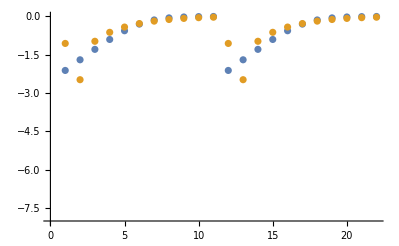

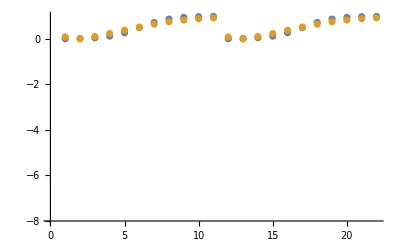

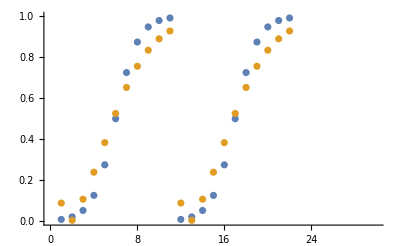

```mathematica
dataSet=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSet,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSet,3]]}, AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]], filteredDataList[[dataSet,3]]}, AxesOrigin->{0,-8}, PlotRange->{{0,30}, {0,1}}]
```

### Parameter Distribution

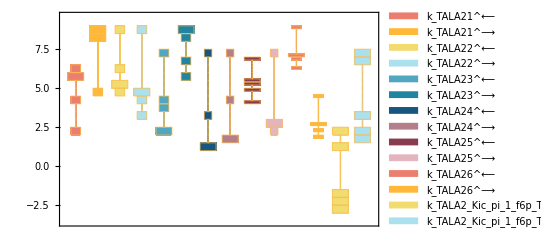

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

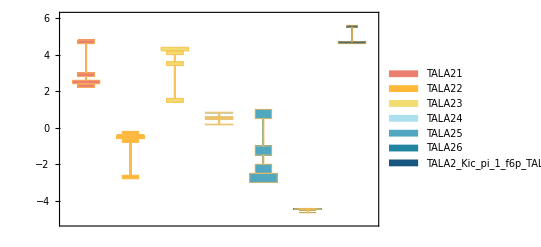

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

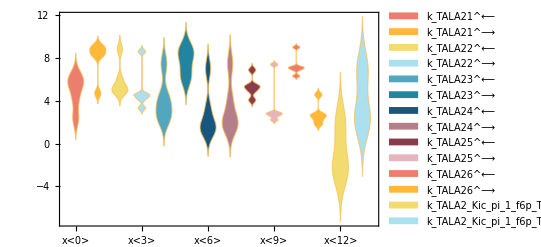

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

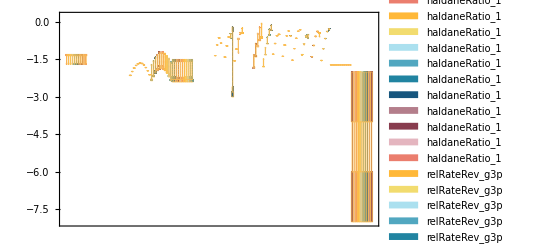

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList[[{1,2,4,5}]], absoluteRateForward/.m["pi","c"]-> 0, absoluteRateReverse/.m["pi","c"]-> 0, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000038 | 0.000035798 | 5.79467
0.00009 | 0.0000219601 | 75.5999
0.0012 | 0.00131506 | 9.58806
0.000285 | 0.000301835 | 5.90696

```mathematica
backCalculateRatios[haldaneRatiosList[[1]][[1]], haldaneRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.840336 | 0.791753 | 5.78138

```mathematica
backCalculateRatios[haldaneRatiosList[[2]][[1]], haldaneRatiosList[[2]][[2]], paramFitSub]//TableForm
```